# Singular Value Decomposition aka SVD

All real m×n matrices have a real SVD A=U Σ Vᵀ.  
	The real square matrix U satisfies Uᵀ U=I_m
	The real square matrix V satisfies Vᵀ V=I_n
	The real m×n diagonal matrix has non-negative and non-increasing diagonal entries σ_1≥σ_2≥…≥σ_(min(m,n))≥0 
The σs are the singular values of the matrix.  The columns of U and V are the left and right singular vectors respectively.  The slightly more involved discussion in https://en.wikipedia.org/wiki/Singular_value_decomposition is generalized to complex A.

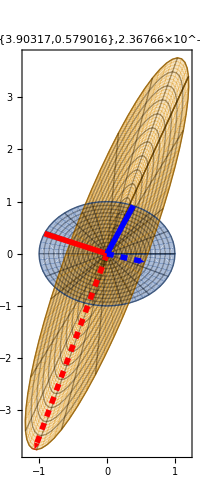

```mathematica
A=({{1.2, 0.1}, {3.4, -1.6}});
{U,S,V}=SingularValueDecomposition[A];
p[r_,θ_]:= r{Cos[θ],Sin[θ]}
ParametricPlot[{p[r,θ], A.p[r,θ]},{r,0,1},{θ,0, 2π},
Mesh->Full,
PlotRange->All,
Epilog->{Thickness[0.01],
{Red,Arrow[{{0,0},V⟦All,1⟧}],Dashed,Arrow[{{0,0},S⟦1,1⟧U⟦All,1⟧}]},
{Blue,Arrow[{{0,0},V⟦All,2⟧}],Dashed,Arrow[{{0,0},S⟦2,2⟧U⟦All,2⟧}]}},
AspectRatio->Automatic,
PlotLabel->{Diagonal[S], Norm[A-U.S.Vᵀ]}]
```

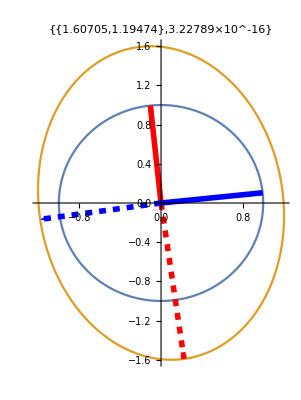

```mathematica
A=({{-1.2, 0.1}, {0, -1.6}});
{U,S,V}=SingularValueDecomposition[A];


ParametricPlot[{p[1,θ], A.p[1,θ]},{θ,0, 2π},
PlotRange->All,
Epilog->{Thickness[0.01],
{Red,Arrow[{{0,0},V⟦All,1⟧}],Dashed,Arrow[{{0,0},S⟦1,1⟧U⟦All,1⟧}]},
{Blue,Arrow[{{0,0},V⟦All,2⟧}],Dashed,Arrow[{{0,0},S⟦2,2⟧U⟦All,2⟧}]}},
AspectRatio->Automatic,
PlotLabel->{Diagonal[S], Norm[A-U.S.Vᵀ,"Frobenius"]}]
```

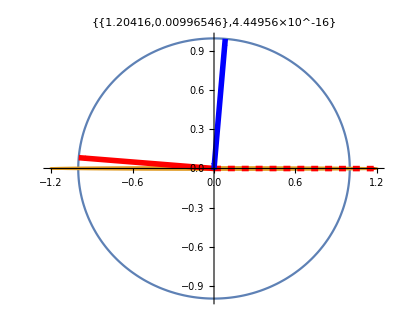

```mathematica
A=({{-1.2, 0.1}, {0, -0.01}});
{U,S,V}=SingularValueDecomposition[A];


ParametricPlot[{p[1,θ], A.p[1,θ]},{θ,0, 2π},
PlotRange->All,
Epilog->{Thickness[0.01],
{Red,Arrow[{{0,0},V⟦All,1⟧}],Dashed,Arrow[{{0,0},S⟦1,1⟧U⟦All,1⟧}]},
{Blue,Arrow[{{0,0},V⟦All,2⟧}],Dashed,Arrow[{{0,0},S⟦2,2⟧U⟦All,2⟧}]}},
AspectRatio->Automatic,
PlotLabel->{Diagonal[S], Norm[A-U.S.Vᵀ,"Frobenius"]}]
```

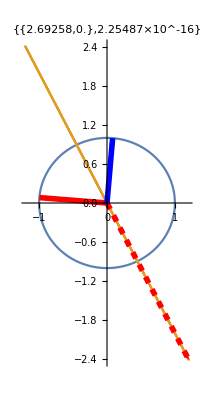

```mathematica
A=({{-1.2, 0.1}, {2.4, -0.2}});
{U,S,V}=SingularValueDecomposition[A];


ParametricPlot[{p[1,θ], A.p[1,θ]},{θ,0, 2π},
PlotRange->All,
Epilog->{Thickness[0.01],
{Red,Arrow[{{0,0},V⟦All,1⟧}],Dashed,Arrow[{{0,0},S⟦1,1⟧U⟦All,1⟧}]},
{Blue,Arrow[{{0,0},V⟦All,2⟧}],Dashed,Arrow[{{0,0},S⟦2,2⟧U⟦All,2⟧}]}},
AspectRatio->Automatic,
PlotLabel->{Diagonal[S], Norm[A-U.S.Vᵀ,"Frobenius"]}]
```

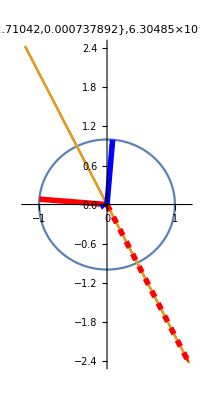

```mathematica
A=({{-1.2, 0.1}, {2.42, -0.2}});
{U,S,V}=SingularValueDecomposition[A];


ParametricPlot[{p[1,θ], A.p[1,θ]},{θ,0, 2π},
PlotRange->All,
Epilog->{Thickness[0.01],
{Red,Arrow[{{0,0},V⟦All,1⟧}],Dashed,Arrow[{{0,0},S⟦1,1⟧U⟦All,1⟧}]},
{Blue,Arrow[{{0,0},V⟦All,2⟧}],Dashed,Arrow[{{0,0},S⟦2,2⟧U⟦All,2⟧}]}},
AspectRatio->Automatic,
PlotLabel->{Diagonal[S], Norm[A-U.S.Vᵀ,"Frobenius"]}]
```

```mathematica
A=({{1.2, 0.1, 2.3}, {3.4, -1.6, 1.2}, {-2.3, 1.0, -5.0}});
{U,S,V}=SingularValueDecomposition[A];
p[r_,θ_,ϕ_]:= r{Cos[θ]Cos[ϕ],Sin[θ]Cos[ϕ], Sin[ϕ]}
Show[
ParametricPlot3D[{p[1,θ,ϕ], A.p[1,θ,ϕ]},
{θ,0, 2π},{ϕ,-π/2,π/2},
Mesh->Full,
PlotStyle->Opacity[0.5],
PlotRange->All],
Graphics3D[{Thickness[0.01],
{Red,Arrow[{{0,0,0},V⟦All,1⟧}],Dashed,Arrow[{{0,0,0},S⟦1,1⟧U⟦All,1⟧}]},
{Blue,Arrow[{{0,0,0},V⟦All,2⟧}],Dashed,Arrow[{{0,0,0},S⟦2,2⟧U⟦All,2⟧}]}}],
PlotLabel->{Diagonal[S], Norm[A-U.S.Vᵀ]}]
```

-Graphics3D-

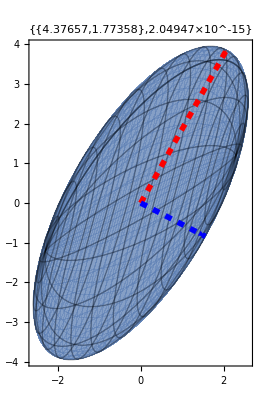

```mathematica
A=({{1.2, 0.1, 2.3}, {3.4, -1.6, 1.2}});
{U,S,V}=SingularValueDecomposition[A];
p[r_,θ_,ϕ_]:= r{Cos[θ]Cos[ϕ],Sin[θ]Cos[ϕ], Sin[ϕ]}
Show[
ParametricPlot[ A.p[1,θ,ϕ],
{θ,0, 2π},{ϕ,-π/2,π/2},
Mesh->Full,
PlotStyle->Opacity[0.5],
PlotRange->All,
Epilog->{Thickness[0.01],
{Red,Dashed,Arrow[{{0,0},S⟦1,1⟧U⟦All,1⟧}]},
{Blue,Dashed,Arrow[{{0,0},S⟦2,2⟧U⟦All,2⟧}]}}],
PlotLabel->{Diagonal[S], Norm[A-U.S.Vᵀ]}]
```

```mathematica
A=({{1.2, 0.1}, {3.4, -1.6}, {-2.3, 1.0}});
{U,S,V}=SingularValueDecomposition[A];
p[r_,θ_]:= r{Cos[θ],Sin[θ]}
Show[
ParametricPlot3D[A.p[1,θ],
{θ,0, 2π},{ϕ,-π/2,π/2},
Mesh->Full,
PlotStyle->Opacity[0.5],
PlotLabel->Diagonal[S],
PlotRange->All],
Graphics3D[{Thickness[0.01],
{Red,Dashed,Arrow[{{0,0,0},S⟦1,1⟧U⟦All,1⟧}]},
{Blue,Dashed,Arrow[{{0,0,0},S⟦2,2⟧U⟦All,2⟧}]}}]]
```

-Graphics3D-